# Newton’s Method

### 1D

Covered in Calculus One.  The idea is to solve h[x]=0 you approximate with the tangent line 
	h[x]≈h[x_0]+h'[x_0](x-x_0)
and use the root of this approximation x_1 as your update.  To solve
	h[x]==0
starting from a guess x_0 you simply solve 
	h[x_0]+h'[x_0](x_1-x_0)=0
which gives
	x_1=x_0-h[x_0]/h'[x_0]
Repeating this as necessary is what computers are good at.

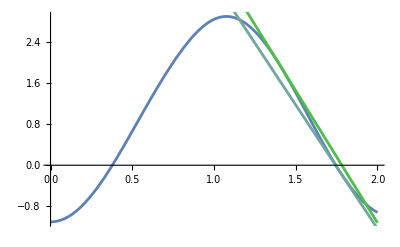

```mathematica
Clear[h,x,n]
h[x_]:= Sin[ ArcTan[E^x^2+Cos[3 x]]]-2 Cos[3 x]
{a,b}={0,2};
x[0]=1.4;
x[n_]:=x[n]=x[n-1]- h[x[n-1]]/h'[x[n-1]]
Show[
Plot[h[x],{x, a, b} ],
Table[
TanLine[x_]=h[x[n]]+h'[x[n]](x-x[n]);
Plot[TanLine[x],{x, a,b},
PlotStyle->RandomColor[]],
{n, 0, 1}]
]
```

### 2D

The idea is to solve {h1[{x,y},h2[{x,y}]}={0,0} which we will write as 
	h[x]=0
with the understanding that h and x are vectors. The linear approximation is 
	h[x_0]+Dh[x_0].(x-x_0)
where Dh[x_0] is a 2×2 matrix.  Our Newton approximation is 
	h[x_0]+Dh[x_0].(x_1-x_0)=0
which has the solution
	x_1=x_0-Dh[x_0]^-1.h[x_0]
Again very easy to code.

{1.03,0.6288}

1.03 | 0.6288
1.05373 | 0.555095
1.05219 | 0.555404
1.05219 | 0.555404
1.05219 | 0.555404
1.05219 | 0.555404
1.05219 | 0.555404
1.05219 | 0.555404

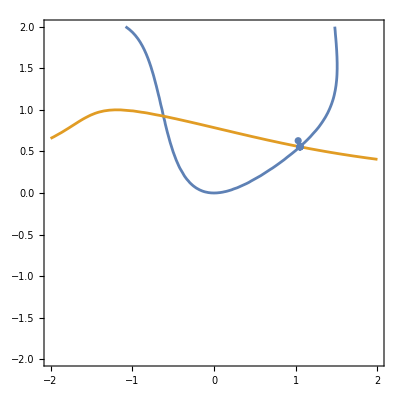

```mathematica
Clear[x,n,y,z,h]
h[{y_,z_}]:= { z-y^2+ Sin[z y], z-Cos[ArcTan[z+y - 0.2 Sin[z y]]]}
Dh[{y_,z_}]=D[h[{y,z}],{{y,z}}];
x[0]={1.03,0.6288}
x[n_]:=x[n]=x[n-1]-LinearSolve[Dh[x[n-1]],h[x[n-1]]]
Data=Table[x[n],{n,0,7}];
TableForm[Data]
Show[
ContourPlot[
{h[{y,z}]⟦1⟧==0,
h[{y,z}]⟦2⟧==0},{y,-2,2},{z,-2,2}
],
ListPlot[Data]
]
```